# Collisionless shear instability growth rate calculator

Version 2025/10/11:
This notebook serves as a supplementary code for Guo et al., 2025.
It is a semi-automatic calculator for the linear growth rate of a collisionless shear instability. 
This notebook solves a simple case with such a shear flow:

v_0(x)=sgn(x)V_0, so γ_0(x)=1/√(1-(V_0/c)^2).
n_e0=n_i0=const., so ω_p=√(n_e0 e^2/m_e ϵ_0 γ_0^3)=const.
B_0=const., so ω_c=eB_0/m_e γ_0=const.
and perturbations in the form of
f(x)exp[i(k_y y+k_z z-ω t)].

To use this calculator, one should run the codes in the “Code” section, and the function “growth[ω_c/ω_p, k_yc/ω_p, k_zc/ω_p, V_0/c]” returns the eigenfrequency with the maximum imaginary part, which corresponds to the most unstable mode found at k=(k_y, k_z) in the shear flow.

In the “Code” section, the variables are normalized with ω_p and c.  V_0→V_0/c, ω_c→ω_c/ω_p, k→kc/ω_p.
*Computation of the magnetized case is time-consuming, so parallel computation on super-computers is recommended if one wants to generate a dispersion relation.

Author: Yao Guo, Key Laboratory for Laser Plasmas, Department of Physics and Astronomy, Shanghai Jiao Tong University.
Email: guoyao2001@sjtu.edu.cn

## Code

```mathematica
wp=1;c=1;
```

```mathematica
growth[B0_,ky1_,kz1_,V0_]:=Which[V0>=1,"Warning: V0/c should be less than 1!",B0==0,f[V0,ky1,kz1],B0!=0,grel[B0,ky1,kz1,V0]];
```

### Magnetized case

```mathematica
Omega[V_]:=w-ky*V;
Drel[V_]:=(w-ky*V)^2*(w^2-(ky^2+kz^2)*c^2-wp^2*gam[V]^2)-wc^2*(w^2-(ky^2+kz^2)*c^2);
Frel[V_]:=1/c^2*((w-ky*V)^2*(w^2-(ky^2+kz^2)*c^2-wp^2*gam[V]^2)^2-wc^2*(w^2-(ky^2+kz^2)*c^2)^2);
gam[V_]:=1/Sqrt[1-V^2/c^2];
eq1[V0_,a_,A_,B_]:=(w^2*(wc^2+wp^2-Omega[V0]^2)+kz^2 c^2(Omega[V0]^2-wc^2+(gam[V0]^2-1)wp^2))*(Omega[V0]^2-wc^2)*(a^2*A)+(w^2/c^2*(wp^2/Omega[V0]^2-1)(Omega[V0]^2-wc^2)+kz^2((V0^2 gam[V0]^2 wp^2)/c^2+(Omega[V0]^2-wc^2)))*Drel[V0]*A+kz (V0 Omega[V0] gam[V0]^2 wp^2-ky c^2(Omega[V0]^2-wc^2))*(Omega[V0]^2-wc^2)*(a^2*B)+wc gam[V0]^2 wp^2(w^2 V0/c^2-w ky-kz^2 V0)*(Omega[V0]^2-wc^2)*a*B+kz^2 V0 gam[V0]^2 wc wp^2*(Omega[V0]^2-wc^2)*a*B+((Omega[V0] kz V0 gam[V0]^2 wp^2)/c^2-ky kz(Omega[V0]^2-wc^2))*Drel[V0]*B==0;
eq2[V0_,a_,A_,B_]:=
(Drel[V0]+c^2 kz^2(Omega[V0]^2-wc^2))a^2*B+(Frel[V0]-c^2 kz^2((c^2(ky^2+kz^2)-w^2)(Omega[V0]^2-wc^2)+gam[V0]^2 Omega[V0]^2 wp^2))/c^2*B+kz(c^2 ky(Omega[V0]^2-wc^2)-V0 gam[V0]^2 Omega[V0] wp^2)a^2*A+
kz^2 V0 gam[V0]^2 wc wp^2*a*A-wc gam[V0]^2 wp^2(ky w+kz^2 V0-w^2 V0/c^2)a*A+
(kz V0 Omega[V0] gam[V0]^2 wp^2(c^2(ky^2+kz^2)-w^2+gam[V0]^2 wp^2)/c^2+ky kz* Drel[V0])A==0;
eq3[V0_]:=((w^2*(wc^2+wp^2-Omega[V0]^2)+kz^2 c^2(Omega[V0]^2-wc^2+(gam[V0]^2-1)wp^2))*(a1*A1+b1*B1)-kz wc wp^2((1-gam[V0]^2)w^2+gam[V0]^2(kz^2 V0^2+ky V0 w))/Omega[V0]*(A1+B1)+kz (V0 Omega[V0] gam[V0]^2 wp^2-ky c^2(Omega[V0]^2-wc^2))*(a1*C1+b1*D1)+wc gam[V0]^2 wp^2(w^2 V0/c^2-w ky-kz^2 V0)*(C1+D1))/Drel[V0]==((w^2*(wc^2+wp^2-Omega[-V0]^2)+kz^2 c^2(Omega[-V0]^2-wc^2+(gam[-V0]^2-1)wp^2))*(a2*A2+b2*B2)-kz wc wp^2((1-gam[-V0]^2)w^2+gam[-V0]^2(kz^2 V0^2-ky V0 w))/Omega[-V0]*(A2+B2)+kz (-V0 Omega[-V0] gam[-V0]^2 wp^2-ky c^2(Omega[-V0]^2-wc^2))*(a2*C2+b2*D2)+wc gam[-V0]^2 wp^2(-w^2 V0/c^2-w ky+kz^2 V0)*(C2+D2))/Drel[-V0];
eq4[V0_]:=((Drel[V0]+c^2 kz^2(Omega[V0]^2-wc^2))*(a1*C1+b1*D1)+kz gam[V0]^2 Omega[V0] wc wp^2*(C1+D1)+kz(c^2 ky(Omega[V0]^2-wc^2)-V0 gam[V0]^2 Omega[V0] wp^2)*(a1*A1+b1*B1)+kz^2 V0 gam[V0]^2 wc wp^2*(A1+B1))/Drel[V0]==((Drel[-V0]+c^2 kz^2(Omega[-V0]^2-wc^2))*(a2*C2+b2*D2)+kz gam[-V0]^2 Omega[-V0] wc wp^2*(C2+D2)+kz(c^2 ky(Omega[-V0]^2-wc^2)+V0 gam[-V0]^2 Omega[-V0] wp^2)*(a2*A2+b2*B2)-kz^2 V0 gam[-V0]^2 wc wp^2*(A2+B2))/Drel[-V0];
```

```mathematica
grel[B0_,ky1_,kz1_,V0_]:=Quiet[(wc=wp*B0; ky=ky1*wp/V0; kz=kz1*wp/V0;(w/.NSolve[{eq1[V0,a1,A1,C1],eq1[V0,b1,B1,D1],eq1[-V0,a2,A2,C2],eq1[-V0,b2,B2,D2],eq2[V0,a1,A1,C1],eq2[V0,b1,B1,D1],eq2[-V0,a2,A2,C2],eq2[-V0,b2,B2,D2],

A1+B1==A2+B2,C1+D1==C2+D2,
If[ky1==0,C1+D1==1,A1+B1==1],eq3[V0],eq4[V0],
Re[a1]<0,Re[b1]<=Re[a1],Re[a2]>0,Re[b2]>=Re[a2],Im[w]>0,Re[w]<=0}])//Union) /.{Union[w]->0}//First[MaximalBy[#,Abs@*Im]]&,MaximalBy::arg1]
```

### Unmagnetized case

```mathematica
a11[V0_]:=(w^2(wp^2-Omega[V0]^2)+kz^2 c^2(Omega[V0]^2+(gam[V0]^2-1)wp^2))/(Omega[V0]^2(w^2-(kz^2+ky^2)c^2-wp^2*gam[V0]^2));
a12[V0_]:=kz*(V0*Omega[V0]*wp^2*gam[V0]^2-ky*c^2*Omega[V0]^2)/(Omega[V0]^2(w^2-(kz^2+ky^2)c^2-wp^2*gam[V0]^2));
a22[V0_]:=1+c^2 kz^2 Omega[V0]^2/(Omega[V0]^2(w^2-(kz^2+ky^2)c^2-wp^2*gam[V0]^2));
kp:=Sqrt[-w^2+(kz^2+ky^2)c^2+wp^2*gam[V0]^2]/c;
wp=1;c=1;
gam[V0_]:=1/Sqrt[1-V0^2/c^2];
Omega[V0_]:=w-ky*V0;
```

```mathematica
f[V0_,ky1_,kz1_]:=Quiet[(ky=ky1*wp/V0; kz=kz1*wp/V0;w/.NSolve[{Det[({{a11[V0]+a11[-V0], a12[V0]+a12[-V0]}, {-a12[V0]-a12[-V0], a22[V0]+a22[-V0]}})]==0,-w^2+(ky^2+kz^2)c^2+wp^2*gam[V0]^2>0,Im[w]>0},Complexes])/.{w->0}//First[MaximalBy[#,Abs@*Im]]&,MaximalBy::arg1]
```

## Example

```mathematica
(*This gives the growth rate of a single mode*)
```

```mathematica
growth[0,1,1,1/2]
```

0.+0.248599 ⅈ

```mathematica
(*This gives the dispersion relation of MI*)
```

```mathematica
List1wc05v=ParallelTable[{j,growth[1,0,j,5/10]},{j,0,5,1/20}];
```

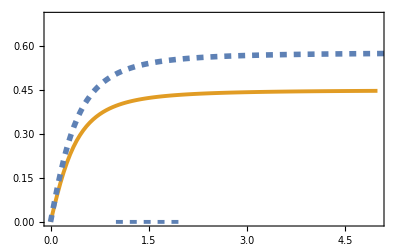

```mathematica
wu[k_,V_]:=1/Sqrt[2]*Sqrt[Sqrt[(4*k^2*V^2)/(1-V^2)+(1+k^2)^2]-(1+k^2)];fig02v=Show[{ListLinePlot[{{0,0},{Re[#1],Im[#2]}&@@@List1wc05v},Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->{{0,5},{0,0.7}},PlotMarkers->None,PlotLegends->Placed[LineLegend[{Style["",FontSize->13],Style["",FontSize->13]},"Spacings"->0.1,LegendMarkerSize->{22,13},LegendLayout->{"Column",1}],{0.7,0.48}],PlotStyle->{{Dashed,Thickness[0.007]},Thickness[0.007],Thickness[0.007],Thickness[0.007],Thickness[0.007],Thickness[0.007],Thickness[0.007]},FrameLabel->{Style["",Black,FontSize->15],Style["",Black,FontSize->15]},FrameTicksStyle->Directive[Black,16],Epilog->{Text[Style[Framed[""],FontSize->14],{2.65,0.20}]}],Plot[wu[x/0.5,0.5],{x,0,10},PlotStyle->{Dashed,Thickness[0.01]},PlotRange->Full]}]
```

```mathematica
(*This gives the dispersion relation of an coupled instability*)
```

```mathematica
List0wc05v=ParallelTable[{i,j,growth[0,i,j,5/10]},{i,0,2,1/10},{j,0,2,1/10}];
```

```mathematica
ListPlot3D[{{Re[#1],Re[#2],Im[#3]}&@@@Flatten[List0wc05v,1]},AxesStyle->Directive[Black,15,Thick],AxesEdge->{True,True,True,True,True,True},PlotRange->{{0,1.4},Full,Full},AxesLabel->{Style["",Black,FontSize->15],Style["",Black,FontSize->15],None},Epilog->{Inset[Style["",Black,FontSize->15],Scaled[{0.3,0.37}],(*调整位置，这里是一个示例值*)Background->None],Inset[Style[Framed[""],Black,FontSize->15],Scaled[{0.75,0.77}]]},ColorFunction->"TemperatureMap",BoundaryStyle->Directive[Red, Thick],Ticks->{{{0.25,"",0.01},0.5,{0.75,"",0.01},1,{1.25,"",0.01},{1.4,"",0.01},2,3},{{0,0},{0.5,"",0.01},1,{1.5,"",0.01},2,{2.5,"",0.01},3},{{0.1,"",0.01},0.2,{0.3,"",0.01},0.4,{0.5,"",0.01},0.6}}]
```

-Graphics3D-